## Generating or Importing Data in Mathematica (with a Halloween twist)

## Experimentally determining Pi

To learn how to analyse data, let’s first generate our own data.
Imagine you have a circular dart disk hanging on a wall in a square frame whose side length is exactly the diameter of your circle.

Visualization of the dart disk and square frame. The corners of the Rectangle are at {-1,-1} and {1,1} and the Disk is centered at {0,0} with a radius of 1.

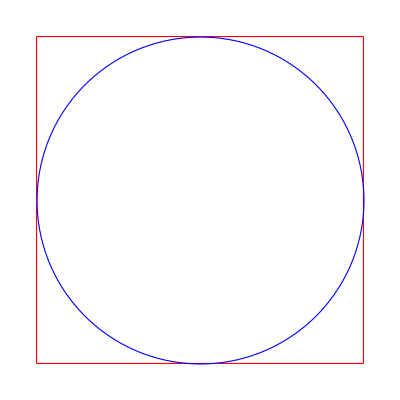

```mathematica
Graphics[{FaceForm[None],EdgeForm[Thick]
,{EdgeForm[Red],Rectangle[{-1,-1},{1,1}]},{EdgeForm[Blue],Disk[{0,0},1]}}]
```

Next, you also have created a robot that throws darts at your dart disk, however, you must have made a mistake, because it always hits within the square, but where in the square is totally random.
So how can this help us estimate pi? We know that the Area of the circle is A_c=π r^2. Since r=1,  A_c= π m^2. The area of the square is A_c=l^2=4 m^2. So the ratio of area of the square that is taken up by the circle is n=π/4.We can’t measure π directly, but we can measure the ratio n and multiply it with 4 to get an experimental measurement of π.
So let’s throw some darts.

Generate Random pairs of coordinates between -1 and 1 in an array of dimensions 10,2:

```mathematica
RandomReal[{-1,1},{10,2}]
```

{{-0.345146,-0.319406},{0.076975,0.702766},{-0.420885,0.464353},{-0.454833,0.71356},{-0.254127,0.687617},{-0.25982,-0.374494},{0.951379,0.849667},{0.152478,0.167279},{-0.572738,-0.54351},{0.567584,0.313633}}

What we are actually interested in is not the coordinates themselves, but whether they lie inside of the circle or not. For this we can use the construct of a “pure function”, check out the tutorial to learn more about them, for now you need to know that you are using &/@ to apply the function to every element in a list (like a For loop in python) and # to represent where in your function that list element should go.

See if the coordinates are members of the region described by the list.

```mathematica
RegionMember[Disk[],#]&/@RandomReal[{-1,1},{10,2}]
```

{True,True,True,True,True,True,True,False,True,True}

Now we need to count how many of the darts landed inside of the circle (aka. the condition is true) and divide that number by the total number of darts to get the ratio n.

```mathematica
Count[RegionMember[Disk[],#]&/@RandomReal[{-1,1},{10,2}],True]/10
```

9/10

Multiplying this by 4 should give us an estimate of pi. To get a numeric Answer, we apply N around the entire expression. (note that the answers will vary every time you run this, since it is generating new coordinates)

```mathematica
N[4*Count[RegionMember[Disk[],#]&/@RandomReal[{-1,1},{10,2}],True]/10]
```

2.4

That’s a pretty terrible estimate, but what if we run our experiment for many more iterations?

```mathematica
N[4*Count[RegionMember[Disk[],#]&/@RandomReal[{-1,1},{100000,2}],True]/100000]
```

3.13024

With 100 000 darts we arrive at a value much closer to pi.

## Analysing data

After this example of how to run a simulation to generate data, let’s learn how to deal with data that already exists.
Usually, you would download data (for example in a csv file) and use the Import function to get it into Mathematica. As an example I will be using 538’s Halloween Candy Rankings. They have many more datasets you can use to practice here: https://data.fivethirtyeight.com/
The one we are looking at asked random people on the internet to choose between two randomly paired up candy bars. Let’s see what is the internet’s favorite Halloween treat.
 Since the file path will be different on everyone’s laptop, I downloaded a dataset on candy bar ratings and exported it onto the Wolfram Cloud as a public file, so you can easily download it again. You have a limited amount of Cloud Credits, once you start using them to run applications, etc. but you don’t have to worry about it for now.

```mathematica
candyData=Import["C:\\Users\\rbc15\\Desktop\\Minerva\\second year\\work-study\\MathematicaTeachingMaterials\\candy-data.csv","CSV"];
CloudExport[candyData,"CSV",Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/objects/6856f005-68b9-4ac0-80b6-c16957cd8a45]

Now you can download the file. One way to get a easy overview, is importing the data as a Dataset.

```mathematica
Dataset[Import[CloudObject[["https://www.wolframcloud.com/objects/cce65bbd-6f6e-4a5f-ad80-8157927e3f35"](https://www.wolframcloud.com/objects/cce65bbd-6f6e-4a5f-ad80-8157927e3f35)]]]
```

Dataset[<>]

The Import function imports everything as a string or a number. However, we can see that there are various types of data like percentages, or Boolean true or false. The Wolfram Language can interpret a number of different data types. Run the cell below to look at all of them.

```mathematica
$InterpreterTypes
```

We can make use of those with SemanticImport. The second input is a list of the data types we have in our dataset. Now you can also click on the heading of each category and see just that row.

```mathematica
candyData=SemanticImport[CloudObject[["https://www.wolframcloud.com/objects/cce65bbd-6f6e-4a5f-ad80-8157927e3f35"](https://www.wolframcloud.com/objects/cce65bbd-6f6e-4a5f-ad80-8157927e3f35)],{"String","Boolean","Boolean","Boolean","Boolean","Boolean","Boolean","Boolean","Boolean","Boolean","Percent","Percent","Percent"}]
```

Dataset[<>]

You can easily get an overview about the type of data available. To access specific elements of the data use indexing just as you would for an array.

Get all available data for the 5th type of candy (Air Heads).

```mathematica
candyData[[5,All]]
```

Dataset[<>]

So what candy is going to make you the most popular today?
The winner is.... Reese’s Peanut Butter cup, followed by a lot of other chocolate bars

```mathematica
Reverse[candyData[SortBy["winpercent"],{"competitorname","winpercent"}]]
```

Dataset[<>]

To access specific parts of the data, for example all the elements that have chocolate in them, you can use Select

```mathematica
candyData[Select[#chocolate&],{"competitorname","winpercent"}]
```

Dataset[<>]

### Bonus: Importing weird file formats

Import the famous Utah Teapot in the 3D file format STL

```mathematica
Import["https://upload.wikimedia.org/wikipedia/commons/9/93/Utah_teapot_(solid).stl","STL"]
```

-Graphics3D-

Note: this is not just a picture, but a 3D graphic. Click and drag to rotate it.